```mathematica
{X==((Abs[a])^((-1))*((Sin[t]*(((a)^(4)+((Cos[t])^(2)*(((a)^(4)*(-1))+(b)^(4)))))^(1/2))+(Cos[t]*(b)^(2)))*(((a)^(2)+((Cos[t])^(2)*(((a)^(2)*(-1))+(b)^(2)))))^((-1))*(a)^(2)),Y==((Abs[b])^((-1))*((Sin[t]*(a)^(2))+(Cos[t]*(((a)^(4)+((Cos[t])^(2)*(((a)^(4)*(-1))+(b)^(4)))))^(1/2)*(-1)))*(((a)^(2)+((Cos[t])^(2)*(((a)^(2)*(-1))+(b)^(2)))))^((-1))*(b)^(2))}
```

{X==(a^2 (b^2 Cos[t]+√(a^4+(-a^4+b^4) Cos[t]^2) Sin[t]))/(Abs[a] (a^2+(-a^2+b^2) Cos[t]^2)),Y==(b^2 (-Cos[t] √(a^4+(-a^4+b^4) Cos[t]^2)+a^2 Sin[t]))/(Abs[b] (a^2+(-a^2+b^2) Cos[t]^2))}

```mathematica
FullSimplify[(a^2 (b^2 Cos[t]+√(a^4+(-a^4+b^4) Cos[t]^2) Sin[t]))/(a(a^2+(-a^2+b^2) Cos[t]^2))]
```

```mathematica
(a (b^2 Cos[t]+√(a^4+(-a^4+b^4) Cos[t]^2) Sin[t]))/(a^2+(-a^2+b^2) Cos[t]^2)/.{a->4,b->3}
```

(4 (9 Cos[t]+√(256-175 Cos[t]^2) Sin[t]))/(16-7 Cos[t]^2)

```mathematica
(b^2 (-Cos[t] √(a^4+(-a^4+b^4) Cos[t]^2)+a^2 Sin[t]))/(b(a^2+(-a^2+b^2) Cos[t]^2))//FullSimplify
```

```mathematica
(b (-Cos[t] √(a^4+(-a^4+b^4) Cos[t]^2)+a^2 Sin[t]))/(a^2+(-a^2+b^2) Cos[t]^2)/.{a->4,b->3}
```

(3 (-Cos[t] √(256-175 Cos[t]^2)+16 Sin[t]))/(16-7 Cos[t]^2)

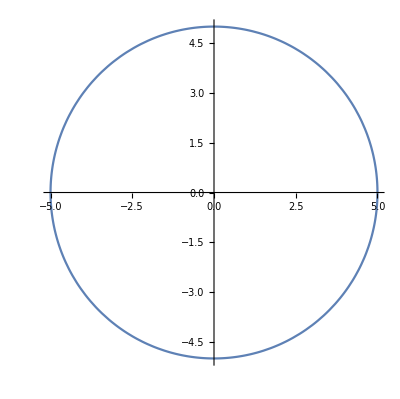

```mathematica
ParametricPlot[{(4 (9 Cos[t]+√(256-175 Cos[t]^2) Sin[t]))/(16-7 Cos[t]^2),(3 (-Cos[t] √(256-175 Cos[t]^2)+16 Sin[t]))/(16-7 Cos[t]^2)},{t,0,2Pi}]
```

```mathematica
Eliminate[{x==(4 (9 Cos[t]+√(256-175 Cos[t]^2) Sin[t]))/(16-7 Cos[t]^2),y==(3 (-Cos[t] √(256-175 Cos[t]^2)+16 Sin[t]))/(16-7 Cos[t]^2)},t]
```

Eliminate::ifun: Eliminate 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

y^2==25-x^2

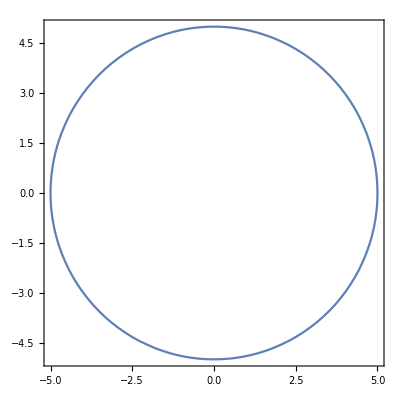

```mathematica
ContourPlot[y^2==25-x^2,{x,-5,5},{y,-5,5}]
```

```mathematica
Show[%9,Axes->True]
```

-Graphics-

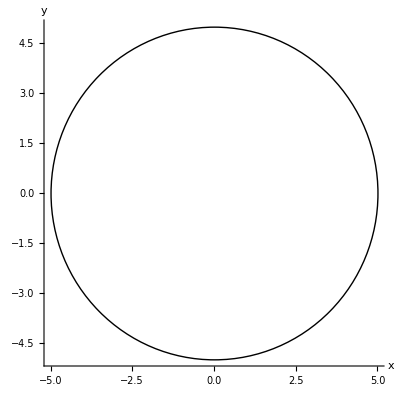

```mathematica
Show[Graphics[Circle[{0,0},5],Axes->True,AxesLabel->{x,y},LabelStyle->Orange]]
```

```mathematica
Subscript[ℛ, 1]=ImplicitRegion[y^2+x^2==25,{x,y}];
Subscript[ℛ, 2]=Circle[{0,0},√(3^2+4^2)];
```

```mathematica
RegionEqual[Subscript[ℛ, 1],Subscript[ℛ, 2]]
```

True